```mathematica
Subscript[δ, a_,b_]:=KroneckerDelta[a,b]
Subscript[A, x_,a_]:=Subscript[δ, x,0] Subscript[δ, a,0]{{1,0},{0,0}}+Subscript[δ, x,0] Subscript[δ, a,1]{{0,0},{0,1}} + Subscript[δ, x,1] Subscript[δ, a,0](1/2*{{1,1},{1,1}})+Subscript[δ, x,1] Subscript[δ, a,1](1/2*{{1,-1},{-1,1}})
CC[i_,j_,q_]:=1/8(∑_(a=0)^1 (Subscript[δ, i,a](∑_(x=0)^1 Subscript[A, x,a])+Subscript[δ, j,a](∑_(x=0)^1 Subscript[A, x,BitXor[a,x]])))-q/4(2-Subscript[δ, i,2]-Subscript[δ, j,2])IdentityMatrix[2]
```

```mathematica
BC[q_]:=2*Max[Table[Eigenvalues[CC[i,j,q]],{i,0,2},{j,0,2}]]
```

```mathematica
η[q_]:=BC[q]/((1/2(1+1/(√2)))-q)
```

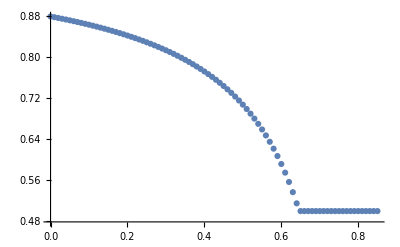

```mathematica
ListPlot[Monitor[Table[{q,η[q]},{q,0,(1/2(1+1/(√2))),0.01}],Row[{ProgressIndicator[q,{0,(1/2(1+1/(√2)))}],q}," "]]]
```